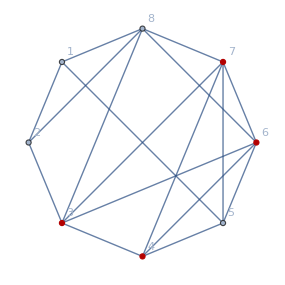
```mathematica
g=-Graphics-
```

-Graphics-

```mathematica
ChromaticPolynomial[g,x]
```

-468 x+1428 x^2-1795 x^3+1231 x^4-504 x^5+124 x^6-17 x^7+x^8

```mathematica
ChromaticPolynomial[g,4]
```

48

```mathematica
BipartiteGraphQ[g]
```

False

```mathematica
PlanarGraphQ[g]
```

False

```mathematica
FindClique[g]
```

{{3,4,6,7}}

```mathematica
EdgeList[g]
```

{1<->2,2<->3,3<->4,4<->5,5<->1,6<->7,6<->8,7<->8,3<->6,5<->6,3<->7,3<->8,5<->7,4<->6,2<->8,4<->7,1<->8}

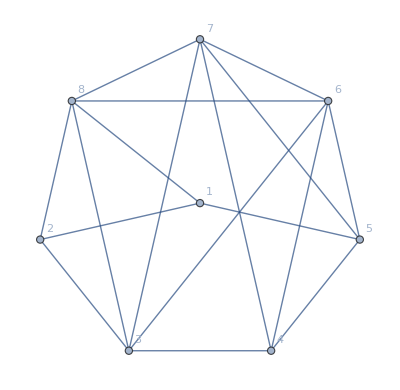

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,6<->7,6<->8,7<->8,3<->6,5<->6,3<->7,3<->8,5<->7,4<->6,2<->8,4<->7,1<->8},GraphLayout->"StarEmbedding",VertexLabels->"Name"]
```

```mathematica
EdgeCount[g]
```

17

```mathematica
Table[n->ChromaticPolynomial[g,n],{n,0,10}]
```

{0→0,1→0,2→0,3→0,4→48,5→3360,6→43200,7→288960,8→1327200,9→4753728,10→14253120}

```mathematica
Booga[]:=Block[{n=8,
trianglePartitions,
edgeAssoc,
covered,
subsets,edgeTrial,coverLength
},
trianglePartitions=FindTrianglePatternPartitionsAtLevel4[n];
edgeAssoc = EdgeToPartition2[trianglePartitions];
Print["number of nodes ", n," triangle partitions : ", Length[trianglePartitions]];
edgeTrial={6<->7,6<->8,7<->8,3<->6,5<->6,3<->7,3<->8,5<->7,4<->6,2<->8,4<->7,1<->8};
covered = Flatten[Table [edgeAssoc[edge23],{edge23,edgeTrial}],1];
Print[TableForm[Sort[Map[SymbolToLabel[ SetsToSymbol[#]]<->Intersection[edgeTrial,EdgesFromPartition[#]]&,DeleteDuplicates[covered]],Length[#1[[2]]]<Length[#2[[2]]]&]]];
covered=Map[SymbolToLabel[ SetsToSymbol[#]]&,trianglePartitions];
Print[Sort[covered]];
covered=DeleteDuplicates[covered];
coverLength=Length[covered];
Print[coverLength];
If[coverLength==Length[trianglePartitions],
With[{g=Graph[Range[n],Join[{1<->2,2<->3,3<->4,4<->5,5<->1},edgeTrial]]},
If[ ConnectedGraphQ[g]&& Length[First[FindClique[g]]]<5,
Print[edgeTrial, "   ",Length[covered], "  " , PlanarGraphQ[Graph[covered]], "    ", 
{Labeled[
Graph[g,GraphHighlight->First[FindClique[g]],GraphLayout->"CircularEmbedding",VertexLabels->"Name",ImageSize->300],
{EdgeCount[g],3*VertexCount[g]-6}],FindClique[g]}
];
]
];
;
];

]
```

number of nodes 8 triangle partitions : 185

148♁27♁35♁6<->{1<->8}
148♁26♁35♁7<->{1<->8}
147♁26♁35♁8<->{4<->7}
16♁247♁35♁8<->{4<->7}
13♁247♁58♁6<->{4<->7}
17♁248♁35♁6<->{2<->8}
16♁248♁35♁7<->{2<->8}
146♁27♁35♁8<->{4<->6}
17♁246♁35♁8<->{4<->6}
13♁246♁58♁7<->{4<->6}
13♁257♁48♁6<->{5<->7}
14♁27♁358♁6<->{3<->8}
14♁26♁358♁7<->{3<->8}
17♁24♁358♁6<->{3<->8}
16♁24♁358♁7<->{3<->8}
137♁25♁48♁6<->{3<->7}
137♁24♁58♁6<->{3<->7}
13♁256♁48♁7<->{5<->6}
136♁25♁48♁7<->{3<->6}
136♁24♁58♁7<->{3<->6}
14♁26♁35♁78<->{7<->8}
16♁24♁35♁78<->{7<->8}
14♁27♁35♁68<->{6<->8}
17♁24♁35♁68<->{6<->8}
14♁267♁35♁8<->{6<->7}
167♁24♁35♁8<->{6<->7}
13♁25♁48♁67<->{6<->7}
13♁24♁58♁67<->{6<->7}
18♁247♁35♁6<->{1<->8,4<->7}
147♁28♁35♁6<->{2<->8,4<->7}
147♁258♁3♁6<->{2<->8,4<->7}
13♁258♁47♁6<->{2<->8,4<->7}
146♁28♁35♁7<->{2<->8,4<->6}
18♁246♁35♁7<->{1<->8,4<->6}
146♁258♁3♁7<->{2<->8,4<->6}
13♁258♁46♁7<->{2<->8,4<->6}
148♁257♁3♁6<->{1<->8,5<->7}
13♁248♁57♁6<->{2<->8,5<->7}
146♁257♁3♁8<->{4<->6,5<->7}
13♁257♁46♁8<->{4<->6,5<->7}
13♁246♁57♁8<->{4<->6,5<->7}
147♁25♁38♁6<->{3<->8,4<->7}
146♁25♁38♁7<->{3<->8,4<->6}
14♁257♁38♁6<->{3<->8,5<->7}
147♁2♁358♁6<->{3<->8,4<->7}
146♁2♁358♁7<->{3<->8,4<->6}
1♁247♁358♁6<->{3<->8,4<->7}
1♁246♁358♁7<->{3<->8,4<->6}
148♁25♁37♁6<->{1<->8,3<->7}
137♁248♁5♁6<->{2<->8,3<->7}
146♁25♁37♁8<->{3<->7,4<->6}
137♁25♁46♁8<->{3<->7,4<->6}
137♁246♁5♁8<->{3<->7,4<->6}
14♁258♁37♁6<->{2<->8,3<->7}
137♁258♁4♁6<->{2<->8,3<->7}
14♁26♁357♁8<->{3<->7,5<->7}
16♁24♁357♁8<->{3<->7,5<->7}
14♁256♁38♁7<->{3<->8,5<->6}
14♁256♁37♁8<->{3<->7,5<->6}
137♁256♁4♁8<->{3<->7,5<->6}
137♁24♁56♁8<->{3<->7,5<->6}
148♁256♁3♁7<->{1<->8,5<->6}
13♁248♁56♁7<->{2<->8,5<->6}
147♁256♁3♁8<->{4<->7,5<->6}
13♁256♁47♁8<->{4<->7,5<->6}
13♁247♁56♁8<->{4<->7,5<->6}
148♁25♁36♁7<->{1<->8,3<->6}
136♁248♁5♁7<->{2<->8,3<->6}
147♁25♁36♁8<->{3<->6,4<->7}
136♁25♁47♁8<->{3<->6,4<->7}
136♁247♁5♁8<->{3<->6,4<->7}
14♁258♁36♁7<->{2<->8,3<->6}
136♁258♁4♁7<->{2<->8,3<->6}
14♁257♁36♁8<->{3<->6,5<->7}
136♁257♁4♁8<->{3<->6,5<->7}
136♁24♁57♁8<->{3<->6,5<->7}
14♁27♁356♁8<->{3<->6,5<->6}
17♁24♁356♁8<->{3<->6,5<->6}
14♁25♁36♁78<->{3<->6,7<->8}
136♁25♁4♁78<->{3<->6,7<->8}
136♁24♁5♁78<->{3<->6,7<->8}
14♁278♁35♁6<->{2<->8,7<->8}
178♁24♁35♁6<->{1<->8,7<->8}
13♁25♁478♁6<->{4<->7,7<->8}
146♁25♁3♁78<->{4<->6,7<->8}
13♁25♁46♁78<->{4<->6,7<->8}
13♁246♁5♁78<->{4<->6,7<->8}
13♁24♁578♁6<->{5<->7,7<->8}
14♁256♁3♁78<->{5<->6,7<->8}
13♁256♁4♁78<->{5<->6,7<->8}
13♁24♁56♁78<->{5<->6,7<->8}
146♁2♁35♁78<->{4<->6,7<->8}
1♁246♁35♁78<->{4<->6,7<->8}
14♁25♁37♁68<->{3<->7,6<->8}
137♁25♁4♁68<->{3<->7,6<->8}
137♁24♁5♁68<->{3<->7,6<->8}
14♁268♁35♁7<->{2<->8,6<->8}
168♁24♁35♁7<->{1<->8,6<->8}
147♁25♁3♁68<->{4<->7,6<->8}
13♁25♁47♁68<->{4<->7,6<->8}
13♁247♁5♁68<->{4<->7,6<->8}
13♁25♁468♁7<->{4<->6,6<->8}
14♁257♁3♁68<->{5<->7,6<->8}
13♁257♁4♁68<->{5<->7,6<->8}
13♁24♁57♁68<->{5<->7,6<->8}
13♁24♁568♁7<->{5<->6,6<->8}
147♁2♁35♁68<->{4<->7,6<->8}
1♁247♁35♁68<->{4<->7,6<->8}
14♁25♁38♁67<->{3<->8,6<->7}
14♁28♁35♁67<->{2<->8,6<->7}
18♁24♁35♁67<->{1<->8,6<->7}
148♁25♁3♁67<->{1<->8,6<->7}
13♁248♁5♁67<->{2<->8,6<->7}
14♁258♁3♁67<->{2<->8,6<->7}
13♁258♁4♁67<->{2<->8,6<->7}
148♁2♁35♁67<->{1<->8,6<->7}
14♁2♁358♁67<->{3<->8,6<->7}
1♁248♁35♁67<->{2<->8,6<->7}
1♁24♁358♁67<->{3<->8,6<->7}
138♁25♁47♁6<->{1<->8,3<->8,4<->7}
138♁247♁5♁6<->{1<->8,3<->8,4<->7}
138♁25♁46♁7<->{1<->8,3<->8,4<->6}
138♁246♁5♁7<->{1<->8,3<->8,4<->6}
138♁257♁4♁6<->{1<->8,3<->8,5<->7}
138♁24♁57♁6<->{1<->8,3<->8,5<->7}
14♁28♁357♁6<->{2<->8,3<->7,5<->7}
18♁24♁357♁6<->{1<->8,3<->7,5<->7}
148♁2♁357♁6<->{1<->8,3<->7,5<->7}
146♁2♁357♁8<->{3<->7,4<->6,5<->7}
1♁248♁357♁6<->{2<->8,3<->7,5<->7}
1♁246♁357♁8<->{3<->7,4<->6,5<->7}
138♁256♁4♁7<->{1<->8,3<->8,5<->6}
138♁24♁56♁7<->{1<->8,3<->8,5<->6}
14♁28♁356♁7<->{2<->8,3<->6,5<->6}
18♁24♁356♁7<->{1<->8,3<->6,5<->6}
148♁2♁356♁7<->{1<->8,3<->6,5<->6}
147♁2♁356♁8<->{3<->6,4<->7,5<->6}
1♁248♁356♁7<->{2<->8,3<->6,5<->6}
1♁247♁356♁8<->{3<->6,4<->7,5<->6}
14♁25♁378♁6<->{3<->7,3<->8,7<->8}
1478♁25♁3♁6<->{1<->8,4<->7,7<->8}
13♁2478♁5♁6<->{2<->8,4<->7,7<->8}
14♁2578♁3♁6<->{2<->8,5<->7,7<->8}
13♁2578♁4♁6<->{2<->8,5<->7,7<->8}
1478♁2♁35♁6<->{1<->8,4<->7,7<->8}
14♁2♁356♁78<->{3<->6,5<->6,7<->8}
1♁2478♁35♁6<->{2<->8,4<->7,7<->8}
1♁24♁356♁78<->{3<->6,5<->6,7<->8}
14♁25♁368♁7<->{3<->6,3<->8,6<->8}
1468♁25♁3♁7<->{1<->8,4<->6,6<->8}
13♁2468♁5♁7<->{2<->8,4<->6,6<->8}
14♁2568♁3♁7<->{2<->8,5<->6,6<->8}
13♁2568♁4♁7<->{2<->8,5<->6,6<->8}
1468♁2♁35♁7<->{1<->8,4<->6,6<->8}
14♁2♁357♁68<->{3<->7,5<->7,6<->8}
1♁2468♁35♁7<->{2<->8,4<->6,6<->8}
1♁24♁357♁68<->{3<->7,5<->7,6<->8}
138♁25♁4♁67<->{1<->8,3<->8,6<->7}
138♁24♁5♁67<->{1<->8,3<->8,6<->7}
14♁25♁367♁8<->{3<->6,3<->7,6<->7}
1367♁25♁4♁8<->{3<->6,3<->7,6<->7}
1367♁24♁5♁8<->{3<->6,3<->7,6<->7}
1467♁25♁3♁8<->{4<->6,4<->7,6<->7}
13♁25♁467♁8<->{4<->6,4<->7,6<->7}
13♁2467♁5♁8<->{4<->6,4<->7,6<->7}
14♁2567♁3♁8<->{5<->6,5<->7,6<->7}
13♁2567♁4♁8<->{5<->6,5<->7,6<->7}
13♁24♁567♁8<->{5<->6,5<->7,6<->7}
14♁25♁3♁678<->{6<->7,6<->8,7<->8}
13♁25♁4♁678<->{6<->7,6<->8,7<->8}
13♁24♁5♁678<->{6<->7,6<->8,7<->8}
1467♁2♁35♁8<->{4<->6,4<->7,6<->7}
14♁2♁35♁678<->{6<->7,6<->8,7<->8}
1♁2467♁35♁8<->{4<->6,4<->7,6<->7}
1♁24♁35♁678<->{6<->7,6<->8,7<->8}
1378♁25♁4♁6<->{1<->8,3<->7,3<->8,7<->8}
1378♁24♁5♁6<->{1<->8,3<->7,3<->8,7<->8}
14♁2♁3578♁6<->{3<->7,3<->8,5<->7,7<->8}
1♁24♁3578♁6<->{3<->7,3<->8,5<->7,7<->8}
1368♁25♁4♁7<->{1<->8,3<->6,3<->8,6<->8}
1368♁24♁5♁7<->{1<->8,3<->6,3<->8,6<->8}
14♁2♁3568♁7<->{3<->6,3<->8,5<->6,6<->8}
1♁24♁3568♁7<->{3<->6,3<->8,5<->6,6<->8}
14♁2♁3567♁8<->{3<->6,3<->7,5<->6,5<->7,6<->7}
1♁24♁3567♁8<->{3<->6,3<->7,5<->6,5<->7,6<->7}

{1♁24♁35♁678,1♁24♁356♁78,1♁24♁3567♁8,1♁24♁3568♁7,1♁24♁357♁68,1♁24♁3578♁6,1♁24♁358♁67,1♁246♁35♁78,1♁246♁357♁8,1♁246♁358♁7,1♁2467♁35♁8,1♁2468♁35♁7,1♁247♁35♁68,1♁247♁356♁8,1♁247♁358♁6,1♁2478♁35♁6,1♁248♁35♁67,1♁248♁356♁7,1♁248♁357♁6,13♁24♁5♁678,13♁24♁56♁78,13♁24♁567♁8,13♁24♁568♁7,13♁24♁57♁68,13♁24♁578♁6,13♁24♁58♁67,13♁246♁5♁78,13♁246♁57♁8,13♁246♁58♁7,13♁2467♁5♁8,13♁2468♁5♁7,13♁247♁5♁68,13♁247♁56♁8,13♁247♁58♁6,13♁2478♁5♁6,13♁248♁5♁67,13♁248♁56♁7,13♁248♁57♁6,13♁25♁4♁678,13♁25♁46♁78,13♁25♁467♁8,13♁25♁468♁7,13♁25♁47♁68,13♁25♁478♁6,13♁25♁48♁67,13♁256♁4♁78,13♁256♁47♁8,13♁256♁48♁7,13♁2567♁4♁8,13♁2568♁4♁7,13♁257♁4♁68,13♁257♁46♁8,13♁257♁48♁6,13♁2578♁4♁6,13♁258♁4♁67,13♁258♁46♁7,13♁258♁47♁6,136♁24♁5♁78,136♁24♁57♁8,136♁24♁58♁7,136♁247♁5♁8,136♁248♁5♁7,136♁25♁4♁78,136♁25♁47♁8,136♁25♁48♁7,136♁257♁4♁8,136♁258♁4♁7,1367♁24♁5♁8,1367♁25♁4♁8,1368♁24♁5♁7,1368♁25♁4♁7,137♁24♁5♁68,137♁24♁56♁8,137♁24♁58♁6,137♁246♁5♁8,137♁248♁5♁6,137♁25♁4♁68,137♁25♁46♁8,137♁25♁48♁6,137♁256♁4♁8,137♁258♁4♁6,1378♁24♁5♁6,1378♁25♁4♁6,138♁24♁5♁67,138♁24♁56♁7,138♁24♁57♁6,138♁246♁5♁7,138♁247♁5♁6,138♁25♁4♁67,138♁25♁46♁7,138♁25♁47♁6,138♁256♁4♁7,138♁257♁4♁6,14♁2♁35♁678,14♁2♁356♁78,14♁2♁3567♁8,14♁2♁3568♁7,14♁2♁357♁68,14♁2♁3578♁6,14♁2♁358♁67,14♁25♁3♁678,14♁25♁36♁78,14♁25♁367♁8,14♁25♁368♁7,14♁25♁37♁68,14♁25♁378♁6,14♁25♁38♁67,14♁256♁3♁78,14♁256♁37♁8,14♁256♁38♁7,14♁2567♁3♁8,14♁2568♁3♁7,14♁257♁3♁68,14♁257♁36♁8,14♁257♁38♁6,14♁2578♁3♁6,14♁258♁3♁67,14♁258♁36♁7,14♁258♁37♁6,14♁26♁35♁78,14♁26♁357♁8,14♁26♁358♁7,14♁267♁35♁8,14♁268♁35♁7,14♁27♁35♁68,14♁27♁356♁8,14♁27♁358♁6,14♁278♁35♁6,14♁28♁35♁67,14♁28♁356♁7,14♁28♁357♁6,146♁2♁35♁78,146♁2♁357♁8,146♁2♁358♁7,146♁25♁3♁78,146♁25♁37♁8,146♁25♁38♁7,146♁257♁3♁8,146♁258♁3♁7,146♁27♁35♁8,146♁28♁35♁7,1467♁2♁35♁8,1467♁25♁3♁8,1468♁2♁35♁7,1468♁25♁3♁7,147♁2♁35♁68,147♁2♁356♁8,147♁2♁358♁6,147♁25♁3♁68,147♁25♁36♁8,147♁25♁38♁6,147♁256♁3♁8,147♁258♁3♁6,147♁26♁35♁8,147♁28♁35♁6,1478♁2♁35♁6,1478♁25♁3♁6,148♁2♁35♁67,148♁2♁356♁7,148♁2♁357♁6,148♁25♁3♁67,148♁25♁36♁7,148♁25♁37♁6,148♁256♁3♁7,148♁257♁3♁6,148♁26♁35♁7,148♁27♁35♁6,16♁24♁35♁78,16♁24♁357♁8,16♁24♁358♁7,16♁247♁35♁8,16♁248♁35♁7,167♁24♁35♁8,168♁24♁35♁7,17♁24♁35♁68,17♁24♁356♁8,17♁24♁358♁6,17♁246♁35♁8,17♁248♁35♁6,178♁24♁35♁6,18♁24♁35♁67,18♁24♁356♁7,18♁24♁357♁6,18♁246♁35♁7,18♁247♁35♁6}

185

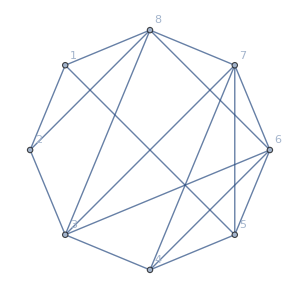
{6<->7,6<->8,7<->8,3<->6,5<->6,3<->7,3<->8,5<->7,4<->6,2<->8,4<->7,1<->8}   185  False    {-Graphics-{17,18},{{3,4,6,7}}}

```mathematica
Booga[]
```

```mathematica
trianglePartitions=FindTrianglePatternPartitionsAtLevel4[8];
edgeAssoc = EdgeToPartition2[trianglePartitions];
```

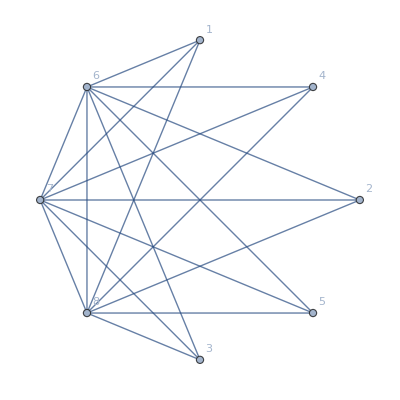

```mathematica
Graph[Keys[edgeAssoc],GraphLayout->"CircularEmbedding",VertexLabels->"Name"]
```

```mathematica
FormulaGraphReverse[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s1]->SetsToSymbol[s2]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]->Rotate[ SymbolToLabel2[ SetsToSymbol[s]],Pi/3],{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
GroupBy[Sort[Map[{SymbolLevel[#],#}&, FindFullFormula[g]]],First]
```

<|4→{{4,v16x27x35x48},{4,v17x26x35x48}},5→{{5,v13x24x58x6x7},{5,v13x25x48x6x7},{5,v13x26x48x5x7},{5,v13x26x4x58x7},{5,v13x27x48x5x6},{5,v13x27x4x58x6},{5,v14x26x35x7x8},{5,v14x26x3x58x7},{5,v14x27x35x6x8},{5,v14x27x3x58x6},{5,v16x24x35x7x8},{5,v16x24x3x58x7},{5,v16x25x3x48x7},{5,v16x27x35x4x8},{5,v16x27x3x48x5},{5,v16x27x3x4x58},{5,v16x2x35x48x7},{5,v17x24x35x6x8},{5,v17x24x3x58x6},{5,v17x25x3x48x6},{5,v17x26x35x4x8},{5,v17x26x3x48x5},{5,v17x26x3x4x58},{5,v17x2x35x48x6},{5,v1x26x35x48x7},{5,v1x27x35x48x6}},6→{{6,v13x24x5x6x7x8},{6,v13x25x4x6x7x8},{6,v13x26x4x5x7x8},{6,v13x27x4x5x6x8},{6,v13x2x48x5x6x7},{6,v13x2x4x58x6x7},{6,v14x25x3x6x7x8},{6,v14x26x3x5x7x8},{6,v14x27x3x5x6x8},{6,v14x2x35x6x7x8},{6,v14x2x3x58x6x7},{6,v16x24x3x5x7x8},{6,v16x25x3x4x7x8},{6,v16x27x3x4x5x8},{6,v16x2x35x4x7x8},{6,v16x2x3x48x5x7},{6,v16x2x3x4x58x7},{6,v17x24x3x5x6x8},{6,v17x25x3x4x6x8},{6,v17x26x3x4x5x8},{6,v17x2x35x4x6x8},{6,v17x2x3x48x5x6},{6,v17x2x3x4x58x6},{6,v1x24x35x6x7x8},{6,v1x24x3x58x6x7},{6,v1x25x3x48x6x7},{6,v1x26x35x4x7x8},{6,v1x26x3x48x5x7},{6,v1x26x3x4x58x7},{6,v1x27x35x4x6x8},{6,v1x27x3x48x5x6},{6,v1x27x3x4x58x6},{6,v1x2x35x48x6x7}},7→{{7,v13x2x4x5x6x7x8},{7,v14x2x3x5x6x7x8},{7,v16x2x3x4x5x7x8},{7,v17x2x3x4x5x6x8},{7,v1x24x3x5x6x7x8},{7,v1x25x3x4x6x7x8},{7,v1x26x3x4x5x7x8},{7,v1x27x3x4x5x6x8},{7,v1x2x35x4x6x7x8},{7,v1x2x3x48x5x6x7},{7,v1x2x3x4x58x6x7}},8→{{8,v1x2x3x4x5x6x7x8}}|>

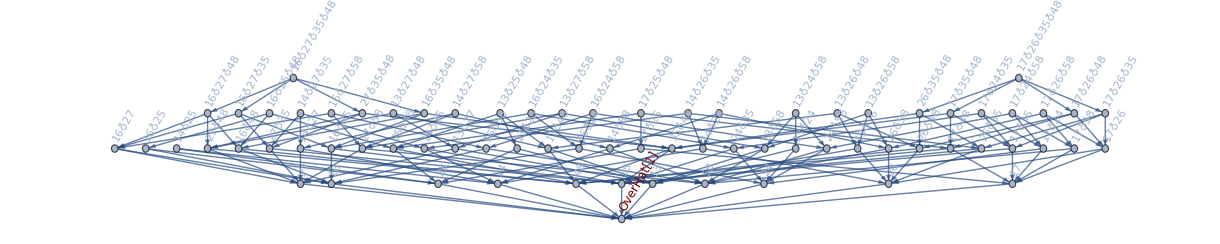

```mathematica
FormulaGraphReverse[FindFullFormula[g]]
```